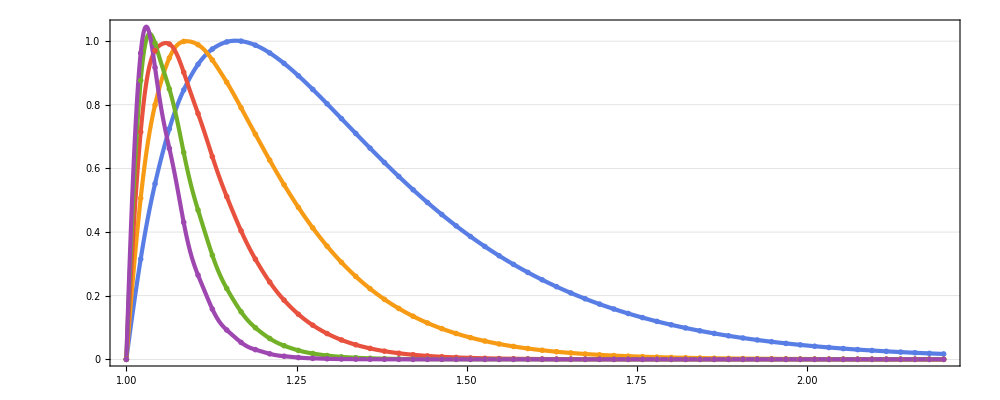

```mathematica
n=1;
freqs={125.,250.,500.,1000.,2000.};
d=(dissonanceMeasure[{#,n}]&/@freqs)//Rescale;

ListLinePlot[d,DataRange->{1,2.2},AspectRatio->1/2.5,PlotRange->All,ImageSize->1000,PerformanceGoal->"Quality",InterpolationOrder->10,PlotTheme->"Business"]
```